```mathematica
SetDirectory[NotebookDirectory[]];
dados=Import["gasideal.dat"]
```

{{6.3,93900},{10.6,95200},{12.9,96200},{15.8,97400},{21.5,99000},{38.,104500},{51.5,107300},{65.5,111900}}

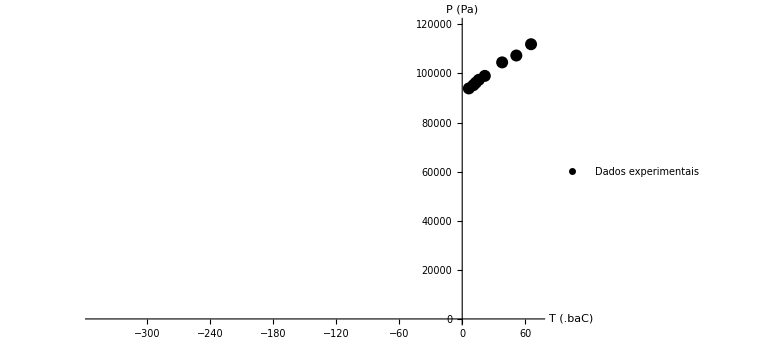

```mathematica
visual={ImageSize->Large,LabelStyle->{Black,Medium}};
plotdados=ListPlot[dados,Evaluate[visual],AxesLabel->{"T (.baC)","P (Pa)"},PlotStyle->{Black,PointSize[0.015]},PlotLegends->{"Dados experimentais"},PlotRange->{{-350,70},{0,120000}}]
```

```mathematica
params=FindFit[dados,a T+b,{{a,300},{b,90000}},T] (*Estimativas de a = 300 e b = 90 000 feitas com base no conjunto de dados*)
```

{a→300.102,b→92343.4}

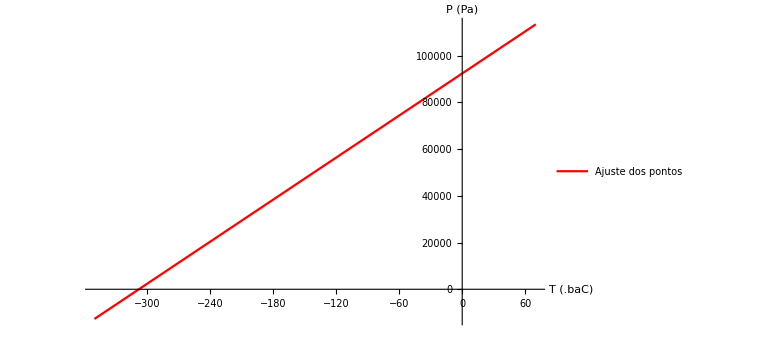

```mathematica
ajuste=Plot[(a T+b)/.params,{T,-350,70},Evaluate[visual],PlotStyle->{Red},PlotLegends->{"Ajuste dos pontos"},AxesLabel->{"T (.baC)","P (Pa)"}]
```

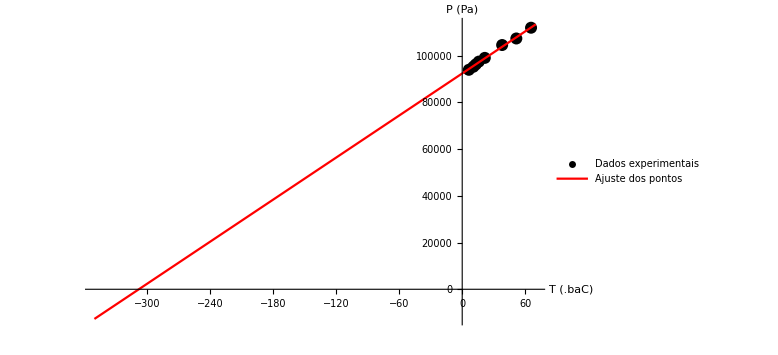

```mathematica
figura=Show[plotdados,ajuste,PlotRange->All]
```

```mathematica
(*Podemos estimar a temperatura do zero absoluto (na qual a pressão se anula) usando a função "Get Coordinates"*)
(*Aplicando essa função ao gráfico, obtemos (aproximadamente) as seguintes coordenadas: *)
{{-307.3939998268591,-5.791703845869051}}

(*E, portanto, nossa estimativa é Subscript[T, 0]=-307.39 .baC, que é um resultado bastante próximo do valor atualmente aceito de -273.15.baC *)
```

{{-307.394,-5.7917}}

```mathematica
(*Faço uma verificação do grau de compatibilidade da estimativa feita com base no erro dos parâmetros a e b*)
nlinAjuste=NonlinearModelFit[dados, a T+b,{{a,300},{b,92000}},T];
nlinAjuste["BestFitParameters"]
nlinAjuste["ParameterErrors"]
nlinAjuste["AdjustedRSquared"]
```

{a→300.102,b→92343.4}

{7.78909,267.236}

0.999981

Impondo P = 0 na relação linear P = a T + b, obtemos T_0=-(b/a). Aplico os novos valores dos parâmetros a e b e desenvolvo uma propagação de incertezas para obter uma estimativa do erro da temperatura T_0 com base nos erros dos parâmetros a e b.

T_0=-(b/a)=-307.7 .baC
σ_T_0=√((∂_a T_0)^2 σ_a^2+(∂_b T_0)^2 σ_b^2)=√((-b/a^2)^2 σ_a^2+(1/a)^2 σ_b^2)= 8.0 .baC

Notemos que |T_0-(-273.15)|=34.55>3*σ_T_0. A princípio isso implica numa inconsistência entre os dois resultados, mas este resultado pode ser desconsiderado nesse nível de análise. Em primeira instância essa discrepância pode ser justificado pela pequena quantidade de pontos experimentais (uma maior quantidade de dados reduziria o valor do erro, é verdade, mas muito provavelmente obteríamos também uma melhor estimativa para T_0), ou ainda por algum efeito de erro sistemático associado ao equipamento de medida que eventualmente acabou interferindo nas medidas do conjunto.